# Wolfram Workshop

## Capítulo 1

## 1. Ingreso de entradas y operaciones básicas

En Wolfram, puedes realizar cálculos simples y complejos.

```mathematica
2+2
```

4

```mathematica
5*3-7.5
```

7.5

```mathematica
(5-3)^(1+2)
```

8

```mathematica
((5-3)^(1+2))/4
```

2

```mathematica
(5-3)^(1+2)/4
```

2

## 2. Funciones incorporadas

Wolfram Language tiene miles de funciones incorporadas.

Máximo común divisor (GCD)

```mathematica
GCD[12,15]
```

3

Gráfico de una función seno

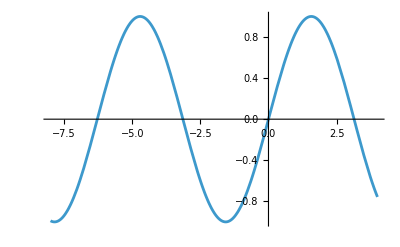

```mathematica
Plot[Sin[x],{x,-8,4}]
```

## 3. Listas y operaciones con listas

Las listas son colecciones ordenadas de elementos. Pueden contener números, variables, cálculos u otras listas.

Máximo común divisor (GCD)

```mathematica
{1,2,3}
```

{1,2,3}

Operaciones con listas

```mathematica
{1,2,3}+2
```

{3,4,5}

Extracción de elementos de una lista

```mathematica
{a,b,c,d}[[3]]
```

c

Creación de una lista con Range

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

## 4. Fracciones y decimales

Wolfram Language maneja fracciones y decimales de manera precisa.

Fracciones exactas

```mathematica
4/3
```

4/3

Simplificación de fracciones con Together

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)

```mathematica
1/x+1/(x+1)+1/(x+2)+1/(x+3)
```

1/x+1/(1+x)+1/(2+x)+1/(3+x)

```mathematica
Together[1/x+1/(x+1)+1/(x+2)+1/(x+3)]
```

(2 (3+11 x+9 x^2+2 x^3))/(x (1+x) (2+x) (3+x))

Conversión a decimales con N

```mathematica
N[4/3]
```

1.33333

Notación científica

```mathematica
ScientificForm[0.00123]
```

1.23×10^-3

## 5. Variables y funciones

Puedes definir variables y funciones personalizadas en Wolfram Language.

Asignación de variables

```mathematica
x=2
1+2x
```

2

5

Borrado de variables

```mathematica
Clear[x]
1+2x
```

1+2 x

```mathematica
x
```

x

Definición de funciones

```mathematica
f[x_]:=1+2x
```

```mathematica
f[x]
f[2]
```

1+2 x

5

Sustitución en expresiones (/.)

```mathematica
1+2x/. x->2
```

5

```mathematica
x^2+7/. x->2
```

11

## ejercicios

### 1. Calcula el resultado de la siguiente expresión:

(3+5)(2-4)^2

```mathematica
(3+5)(2-4)^2
```

32

### 2. Crea una lista con los números del 1 al 20 y luego suma 5 a cada elemento de la lista.

```mathematica
Range[20]+5
```

{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

### 3. Define una función que calcule el cuadrado de un número y luego aplícala al número 7.

```mathematica
f[x_]:=x^2
f[7]
```

49

### 4. Grafica la función coseno desde -10 hasta 10.

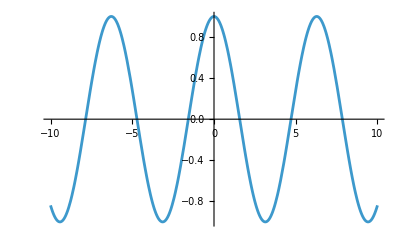

```mathematica
Plot[Cos[x], {x,-10,10}]
```

### 5. Calcula el máximo común divisor (GCD) de 24 y 36.

```mathematica
GCD[24,36]
```

12

## Capítulo 2

## 2.1. Álgebra

Wolfram Language es muy potente para manipular expresiones algebraicas, resolver ecuaciones y trabajar con polinomios.

Factorización de expresiones

```mathematica
Factor[x^2+2x+1]
```

(1+x)^2

Resolución de ecuaciones

```mathematica
Solve[x^2+5x-6==0,x]
```

{{x→-6},{x→1}}

Resolución de sistemas de ecuaciones

```mathematica
Solve[{x^2+5==y,7x-5==y},{x,y}]
```

{{x→2,y→9},{x→5,y→30}}

Uso de Reduce para inecuaciones

```mathematica
Reduce[(x-1)(x-2)(x-3)(x-4)>0,x]
```

x<1||2<x<3||x>4

Visualización de inecuaciones con NumberLinePlot

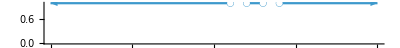

```mathematica
NumberLinePlot[x<1||2<x<3||x>4,{x,-10,10}]
```

## 2.2. Gráficos en 2D

Wolfram Language permite crear gráficos en 2D de funciones, regiones y más.

Gráfico de una función polinómica

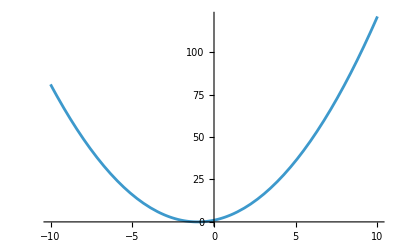

```mathematica
Plot[x^2+2x+1,{x,-10,10}]
```

Gráfico de una región definida por inecuaciones

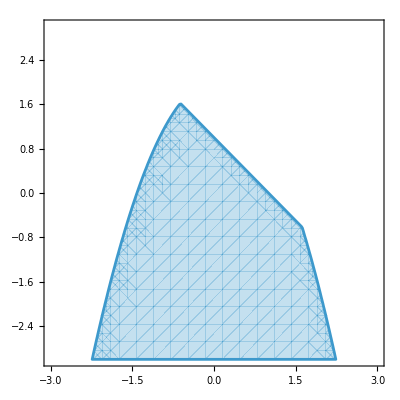

```mathematica
RegionPlot[x^2+y<2&&x+y<1,{x,-3,3},{y,-3,3}]
```

Personalización de gráficos con leyendas

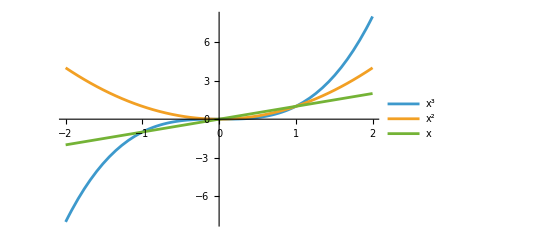

```mathematica
Plot[{x^3,x^2,x},{x,-2,2},PlotLegends->"Expressions"]
```

Rellenar el área bajo una curva

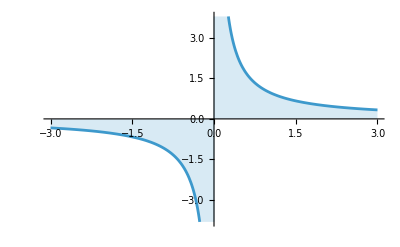

```mathematica
Plot[1/x,{x,-3,3},Filling->Axis]
```

Combinación de gráficos con Show

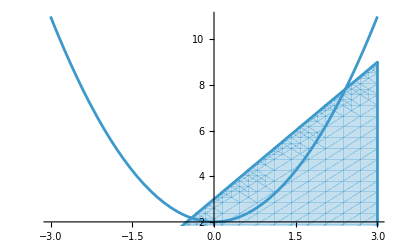

```mathematica
Show[{Plot[x^2+2,{x,-3,3}],RegionPlot[2x>y-3,{x,-3,3},{y,0,9}]}]
```

## 2.3. Geometría

Wolfram Language permite trabajar con formas geométricas en 2D y 3D, calcular áreas, volúmenes y más.

Creación de un círculo



```mathematica
Graphics[Disk[]]
```

```mathematica
Graphics[Disk[{0,0},1]]
```

-Graphics-

Creación de un rectángulo

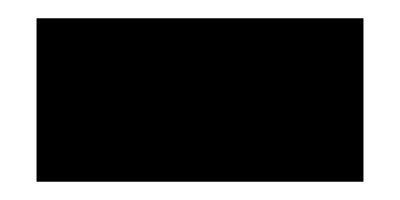

```mathematica
Graphics[Rectangle[{0,0},{4,2}]]
```

Combinación de formas con estilos

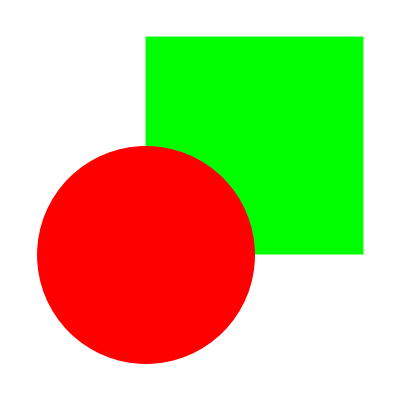

```mathematica
Graphics[{
Green,Rectangle[{0,0},{2,2}],
Red,Disk[]}]
```

Cálculo del área de un triángulo

```mathematica
b=2
h=5
(b×h)/2
```

2

5

5

```mathematica
tr=SASTriangle[1,90°,2]
Area[tr]
```

Triangle[{{0,0},{√5,0},{4/(√5),2/(√5)}}]

1

Visualización de objetos en 3D

```mathematica
Graphics3D[Ball[]]
```

-Graphics3D-

Cálculo del volumen

```mathematica
Volume[Ball[]]
```

(4 π)/3

## 2.4. Trigonometría

Identidades trigonométricas

```mathematica
Sin[x]/Cos[x]==Tan[x]
```

True

Funciones trigonométricas inversas

```mathematica
ArcTan[1]
```

π/4

Expansión de expresiones trigonométricas

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

Resolución de ecuaciones trigonométricas

```mathematica
Solve[Cos[x]^2+Sin[x]^2==x]
```

{{x→1}}

## 2.5. Coordenadas polares

Gráfico polar

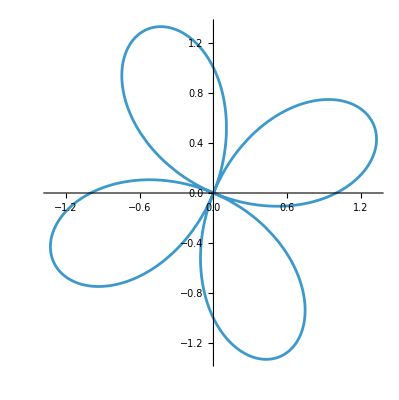

```mathematica
PolarPlot[Sin[2θ]+Cos[2θ],{θ,0,2π}]
```

Conversión de coordenadas cartesianas a polares

```mathematica
ToPolarCoordinates[{1,1}]
```

{√2,π/4}

## 2.6. Funciones exponenciales y logarítmicas

Logaritmo natural

```mathematica
Log[E^2]
```

2

Logaritmo en base 2

```mathematica
Log[2,64]
```

6

Gráfico en escala logarítmica

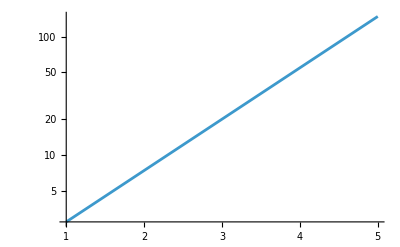

```mathematica
LogPlot[E^x,{x,1,5}]
```

Gráfico con ambos ejes logarítmicos

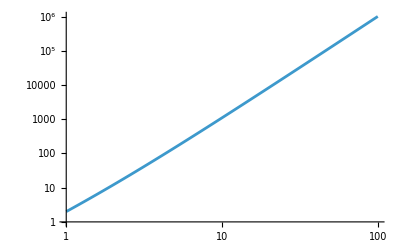

```mathematica
LogLogPlot[x^2+x^3,{x,1,100}]
```

## ejercicios

### 1. Factoriza la expresión

x^3+6 x^2+11x-6

```mathematica
Factor[x^3-6 x^2+11x-6]
```

(-3+x) (-2+x) (-1+x)

### 2. Resuelve el sistema de ecuaciones

{x+y=5
x-y=1

```mathematica
Solve[{x+y==5x-y==1},{x,y}]
```

{{x→1/3,y→2/3}}

### 3. Grafica la función:

y=sin(x)+cos(x),  x∈[0,2π]

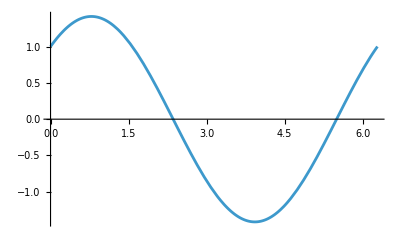

```mathematica
Plot[Sin[x]+Cos[x],{x,0,2π}]
```

### 4. Calcula el área de un círculo con radio 5.

```mathematica
Area[Disk[{0,0},5]]
```

25 π

### 5. Resuelve la ecuación trigonométrica

sin(x)=cos(x),  x∈(0,2π)

```mathematica
Solve[{Sin[x]==Cos[x],0<x<2π},x]
```

{{x→-2 ArcTan[1-√2]},{x→2 π-2 ArcTan[1+√2]}}

## Capítulo 3

límites, derivadas, integrales, secuencias, sumas y series

## 3.1. Límites

Calculo de límites de funciones, tanto en puntos finitos como en el infinito

Cálculo de un límite en un punto

```mathematica
Limit[(x^3-1)/(x-1),x->1]
```

3

```mathematica
lim_(x->1) (x^3-1)/(x-1)
```

3

Cálculo de un límite en el infinito

```mathematica
Limit[(2x^3-1)/(5x^3+x-1),x->Infinity]
```

2/5

```mathematica
Limit[(2 x^3-1)/(5 x^3+x-1),x->∞]
```

2/5

```mathematica
lim_(x->∞) (2 x^3-1)/(5 x^3+x-1)
```

2/5

Límites laterales

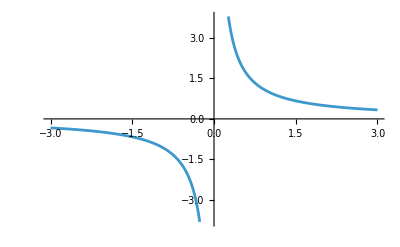

```mathematica
Plot[1/x,{x,-3,3}]
```

```mathematica
lim_(x->0) 1/x
```

Indeterminate

```mathematica
lim_(x->0^-) 1/x
```

-∞

```mathematica
Limit[1/x,x->0,Direction->1]  (*Límite por la izquierda*)
```

-∞

```mathematica
Limit[1/x,x->0,Direction->-1]  (*Límite por la derecha*)
```

∞

```mathematica
lim_(x->0^+) 1/x
```

∞

Limites por arriba/abajo

(|x|)/x,  x∈ℝ

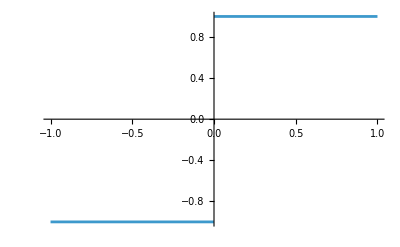

```mathematica
Plot[Abs[x]/x,{x,-1,1}]
```

```mathematica
Limit[Abs[x]/x,x->0,Direction->"FromAbove"]
```

1

```mathematica
Limit[Abs[x]/x,x->0,Direction->"FromBelow"]
```

-1

## 3.2. Derivadas

Derivada de una función

```mathematica
D[x^6,x]
```

6 x^5

Derivada de una función trigonométrica

```mathematica
Sin'[x]
D[Sin[x],x]
```

Cos[x]

Cos[x]

Derivada de una función definida

```mathematica
f[x_]:=x^2+2x+1
f[x]
```

1+2 x+x^2

```mathematica
f'[x]
D[f[x],x]
```

2+2 x

2+2 x

Gráfico de una función y su derivada

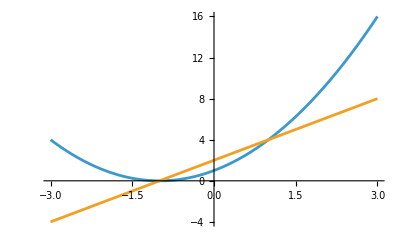

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

Derivadas de orden superior

```mathematica
D[x^6,{x,3}]
```

120 x^3

## 3.3. Integrales

Calculo de integrales, tanto definidas como indefinidas

Integral indefinida

```mathematica
Integrate[8 x^4,x]
```

(8 x^5)/5

```mathematica
∫8 x^4 ⅆx
```

(8 x^5)/5

Integral definida

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

```mathematica
∫_0^π Sin[x]ⅆx
```

2

Aproximación numérica de una integral

```mathematica
∫_0^π (x^3 Sin[x]+2 Log[3x]^2)ⅆx
```

π (-6+π^2+2 (2+Log[3]^2+Log[9] (-1+Log[π])+(-2+Log[π]) Log[π]))

```mathematica
NIntegrate[x^3 Sin[x]+2 Log[3x]^2,{x,0,Pi}]
```

28.1531

## 3.4. Secuencias, sumas y series

Generación de una secuencia

```mathematica
Table[x^2,{x,1,7}]
```

{1,4,9,16,25,36,49}

Secuencia de Fibonacci

```mathematica
Table[Fibonacci[x],{x,1,7}]
```

{1,1,2,3,5,8,13}

Secuencia recursiva

```mathematica
RecurrenceTable[{
a[x]==2 a[x-1],
a[1]==1},
a,
{x,1,8}]
```

{1,2,4,8,16,32,64,128}

Función de generación para una secuencia

```mathematica
FindSequenceFunction[{2,4,6,8},n]
```

2 n

Suma de una secuencia

```mathematica
Sum[i (i+1),{i,1,10}]
```

440

```mathematica
∑_(i=1)^10 i(i+1)
```

440

```mathematica
∑_(i=1)^n ∑_(j=1)^n i j
```

1/4 n^2 (1+n)^2

Serie de potencias (aproximaciones)

e^(x^2)

```mathematica
Series[E^(x^2),{x,0,8}]
```

1+x^2+x^4/2+x^6/6+x^8/24+O[x]^9

Truncamiento de una serie

```mathematica
Normal[Series[E^(x^2),{x,0,8}]]
```

1+x^2+x^4/2+x^6/6+x^8/24

## Representación gráfica

Ecuaciones paramétricas.

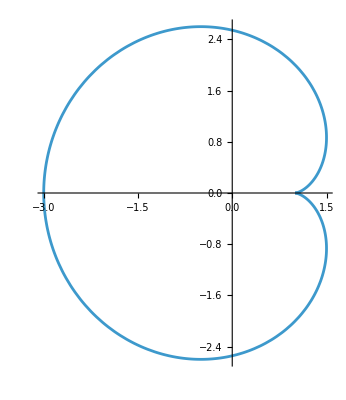

```mathematica
ParametricPlot[{2 Cos[t]-Cos[2 t],2 Sin[t]-Sin[2 t]},{t,0,2 Pi}]
```

```mathematica
Plot3D[Sin[x] Sin[y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

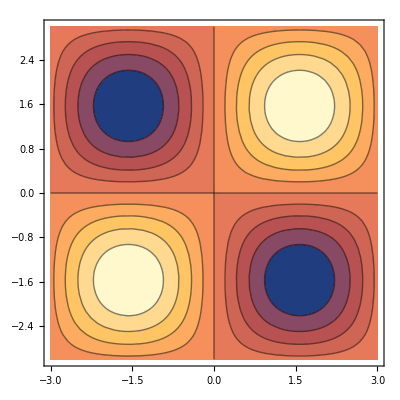

```mathematica
ContourPlot[Sin[x] Sin[y],{x,-3,3},{y,-3,3}]
```

```mathematica
DensityPlot[Sin[x] Sin[y],{x,-4,4},{y,-3,3}]
```

-Graphics-

## ejercicios

### 1. Calcula el límite de la siguiente función cuando x tiende a 0:

f(x)=(sin(x))/x

lim_(x→0) (sin(x))/x

```mathematica
lim_(x->0) Sin[x]/x
```

1

### 2. Calcula la derivada de la función:

f(x)=e^(x^2)

```mathematica
D[E^(x^2),x]
```

2 ⅇ^(x^2) x

### 3. Calcula la integral definida de la función:

f(x)=∫_0^1 x^3 ⅆx

```mathematica
Integrate[x^3,x]
```

x^4/4

```mathematica
∫_0^1 x^3 ⅆx
```

1/4

### 4. Genera una secuencia de los primeros 10 números cuadrados y calcula su suma.

```mathematica
Table[i^2,{i,1,10}]
Total[%]
```

{1,4,9,16,25,36,49,64,81,100}

385

```mathematica
∑_(i=1)^10 i^2
```

385

### 5. Encuentra la serie de potencias de la función:

f(x)=cos(x)

al rededor de x=0, hasta el orden 6.

```mathematica
Series[Cos[x],{x,0,6}]
```

1-x^2/2+x^4/24-x^6/720+O[x]^7